```mathematica
(*Air Balloon Animation*)
Graphics3D[{
(*Ground*)
Green,Cuboid[{0,0,0},{230,100,5}],
(*Sky*)
Blue,Cuboid[{0,100,0},{230,98,150}],
Blue,Cuboid[{0,0,0},{2,100,150}],

(*Air Balloon*)
Red,Scale[Sphere[{24,37,70}],{19,19,15}],
(*Cart Side #1*)
Brown, Cuboid[{17,45,35},{30,46,45}],
(*Cart Side #2*)
Brown, Cuboid[{17,45,35},{16,30,45}],
(*Cart Side #3*)
Brown, Cuboid[{17,30,35},{30,29,45}],
(*Cart Side #4*)
Brown, Cuboid[{30,45,35},{31,30,45}],
(*Cart Base*)
Brown,Cuboid[{17,30,35},{30,45,36}],
(*Rope*)
Black,Tube[{{17,45,45},{15,46,61}}],
Black,Tube[{{17,30,45},{15,28,61}}],
Black,Tube[{{30,45,45},{30,46,61}}],
Black,Tube[{{30,30,45},{30,28,61}}],

(*Head*)
Pink,Sphere[{200,10,30},4],
(*Body*)
White,Cylinder[{{200,10,27},{200,10,15}},2],
(*Arms*)
Pink,Cylinder[{{200,11,25},{195,15,27}},1],
Pink,Cylinder[{{200,9,25},{200,7,20}},1],
(*Legs*)
Pink,Cylinder[{{200,11,27},{200,11,5}}],
Pink,Cylinder[{{200,9,27},{200,9,5}}],




}]

airBalloonAnimation=Manipulate[
Graphics3D[{
(*Ground*)
Green,Cuboid[{0,0,0},{230,100,5}],
(*Sky*)
{RGBColor[0,0,225,0.5],Cuboid[{0,100,0},{230,98,150}]},
{RGBColor[0,0,225,0.5],Cuboid[{0,0,0},{2,100,150}]},

Translate[{
(*Air Balloon Moving*)
{RGBColor[Sin[n Degree],Cos[n Degree],Sin[n Degree]],Scale[Sphere[{24,37,70}],{19,19,15}]},
(*Cart Side #1*)
Brown, Cuboid[{17,45,35},{30,46,45}],
(*Cart Side #2*)
Brown, Cuboid[{17,45,35},{16,30,45}],
(*Cart Side #3*)
Brown, Cuboid[{17,30,35},{30,29,45}],
(*Cart Side #4*)
Brown, Cuboid[{30,45,35},{31,30,45}],
(*Cart Base*)
Brown,Cuboid[{17,30,35},{30,45,36}],
(*Rope*)
Black,Tube[{{17,45,45},{15,46,61}}],
Black,Tube[{{17,30,45},{15,28,61}}],
Black,Tube[{{30,45,45},{30,46,61}}],
Black,Tube[{{30,30,45},{30,28,61}}]},{Piecewise[{{n,n≤160},{160,n>160}}],0,10Sin[n/10]}],


(*Head*)
Pink,Sphere[{200,10,30},4],
(*Body*)
White,Cylinder[{{200,10,27},{200,10,15}},2],
(*Arms waving*)
Rotate[
{Pink,Cylinder[{{200,11,25},{195,15,27}},1]},Cos[n/10],{200,9,25}
],
Rotate[
{Pink,Cylinder[{{200,9,25},{200,7,20}},1]},-n/50,{200,9,25}
],
(*Legs*)
Pink,Cylinder[{{200,11,27},{200,11,5}}],
Pink,Cylinder[{{200,9,27},{200,9,5}}]
},PlotRange-> {{0,250},{0,100},{0,200}},Lighting->"Neutral",Boxed->False],{n,0,100}]
```

-Graphics3D-

```mathematica
SetDirectory["G:\\"]
Export["Chen_Peilin_B1.swf",airBalloonAnimation]
```

G:\

Chen_Peilin_B1.swf

#### Scratch work

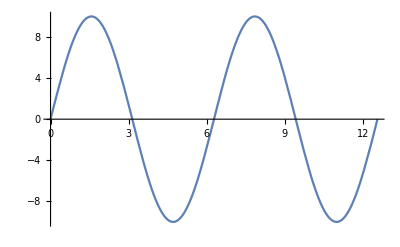

```mathematica
(*Sin Wave #1*)
Plot[10 Sin[x],{x,0,4 π}, PlotRange-> {{0,4π},{-10,10}}]
```